Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j},ϕ_j}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m; and ϕ_j the phase that determines if marbles are able to leave the node or not. When ϕ_j==0 or Sin[ω t+ϕ_j]≥ 0 marbles can leave the node.
Given a network, the rules of the simulation are that at every tick:
	■ One node passes one of its marbles to one of its neighbors. 
	■ The marble is passed if ϕ_j==0∨Sin[ω t+ϕ_i]≥ 0, otherwise the marble stays. 
	■ The node is chosen based on the number of marbles it has (this is, if node’s A has more marbles than node B, it is more likely that the A is chosen).

graphToNet[graph, ini,fun] takes a graph (Mathematica style) and returns a list {{m_1,{n_11,n_12,…,n_(1 N_1)},ϕ_1},…,{m_j,{n_(j 1),n_(j 2),…,n_(j N_j)},ϕ_j},…,{m_N,{n_(N 1),n_(N 2),…,n_(N N_j)},ϕ_N}}; with N the number of nodes in the graph, n_(j s) the s-th neighbour of node j  and ϕ_j determined by fun. 
By default fun is RandomChoice[{9/10,1/20,1/20}→{0,π,2π}], fun fills the phases ϕ_i. 
ini can be one of the following:
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles

```mathematica
graphToNet[g_Graph,ini:{a_,n_},ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#,ϕ[]}&/@nei,{n,1}->a]
]
```

```mathematica
graphToNet[g_Graph,ini_List,ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei,Table[ϕ[],{Length[ini]}]}]
]/;Length[ini]==VertexCount[g]
```

```mathematica
graphToNet[g_Graph,ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],n=VertexCount[g]},
{RandomInteger[n],#,ϕ[]}&/@nei
]
```

netEvolve[graph, ω,T] takes a graph (represented as previously described), with N nodes, an integer T, and a real ω and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.

```mathematica
ω=1/2;
```

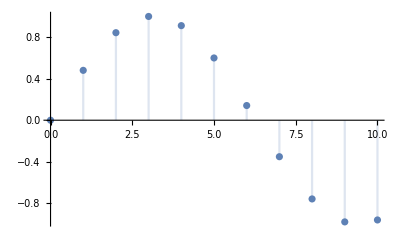

```mathematica
DiscretePlot[Sin[ω t], {t,0,10}]
```

```mathematica
netEvolve[graph_List,ω_Real?Positive,T_Integer]:=Module[
{marbles=graph[[All,1]],nodes=Range[Length[graph]],add,t=0},
add[marbles_List]:=Module[{out=RandomChoice[marbles->nodes],in},
t++;
(*Print[t];*)
If[graph[[out]][[-1]]==0∨Sin[ω t+graph[[out]][[-1]]]>0,
in=RandomChoice[graph[[out,2]]];
(*Print[{out,in}];*)
ReplacePart[marbles,{out->marbles[[out]]-1,in->marbles[[in]]+1}],
marbles
]
];
NestList[add,marbles,T]
]
```

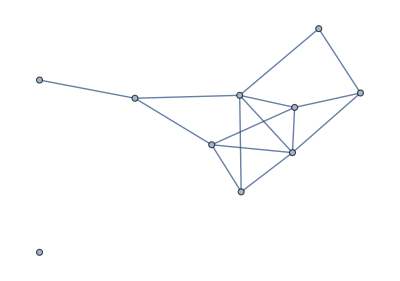

```mathematica
gr=RandomGraph[{10,15}]
```

```mathematica
test=graphToNet[gr,{10,1}]
```

{{10,{2,5,8},0},{0,{1,6,7,8,9},0},{0,{6,7,8},0},{0,{},0},{0,{1,7,8,9},0},{0,{2,3},0},{0,{2,3,5,8},0},{0,{1,2,3,5,7},0},{0,{2,5,10},0},{0,{9},0}}

```mathematica
marbles=netEvolve[test,.5,50];
```

Para mirar el número de pelotas en cada nodo (ejemplo con el nodo 1):

```mathematica
marbles[[All,1]]
```

{10,9,8,7,6,5,4,3,3,3,3,3,3,3,4,3,3,2,2,2,2,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

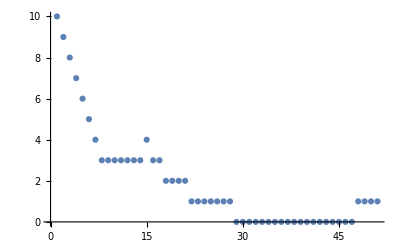

```mathematica
ListPlot[marbles[[All,1]]]
```

El 4, que está solo, permanece constante

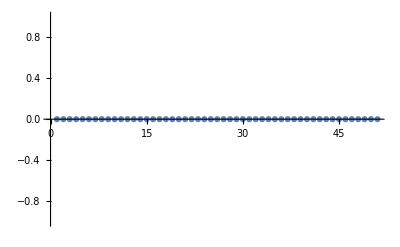

```mathematica
ListPlot[marbles[[All,4]]]
```

El número total de pelotas es

```mathematica
Total/@marbles
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

La densidad de nodos en un tick (el último)

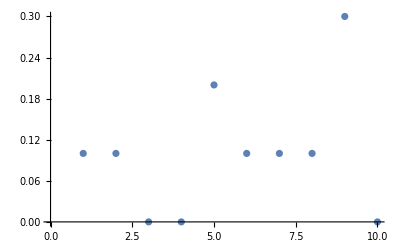

```mathematica
ListPlot[marbles[[-1]]/Total[marbles[[-1]]]]
```

La densidad de nodos en el tiempo

```mathematica
ListPlot3D[marbles/Total[marbles[[-1]]],AxesLabel->{"Node","time",ρ}]
```

-Graphics3D-